```mathematica
Quit[]
```

## Load data

```mathematica
(* Load data first *)
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"cohomology_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,25,
3,19,
4,15];
NumAllStatesUpToLevel[NN_,level_] := Total[#[[9]]&/@Select[cohomology[NN],#[[1]]<=level&]];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
NumMultiGravitonStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,10]];
```

```mathematica
(* Usage example *)
NumAllStates[2,{0,0,4,4,4},7]
NumMultiGravitonStates[2,{0,0,4,4,4},7]
```

1

0

## U(1) partition function

```mathematica
level=25;
ZU1sw[x_,a_,b_,u_,v_,w_]:=(a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b)) x
ZU1B[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]+ZU1sw[-x,a,b,-u,-v,-w])
ZU1F[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]-ZU1sw[-x,a,b,-u,-v,-w])

ZU1[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(ZU1B[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n ZU1F[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
ZU1reduced[x_]:=ZU1[1,x^3,x^3,x^2,x^2,x^2]
IU1reduced[x_]:=ZU1[-1,x^3,x^3,-x^2,-x^2,-x^2]
```

## Partition function

```mathematica
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[1;;2]]]]*Length[Permutations[charges[[3;;5]]]];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[3;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Index[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
Index[NN_] := Index[NN] = Series[(1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UIndex[NN_] := UIndex[NN] = Series[IU1reduced[x] (1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UNumAllStates[NN_] := UNumAllStates[NN] = Series[ZU1reduced[x] (1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

```mathematica
UIndex[2]
```

1+3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+O[x]^26

```mathematica
Index[2]
```

1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25+O[x]^26

## Graviton partition function

```mathematica
level=25;
f[x_,a_,b_,u_,v_,w_]:=(1+ u)(1+ v)(1+  w)/(1-a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- u(1+ v)(1+ w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- v(1+  w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x v)/(1-x w)-1)-w/(1- a)/(1- b)((1+ x a)(1+x b)/(1-x w)-1)-a b x/(1- a)/(1- b)-((a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b))) x

fB[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]+f[-x,a,b,-u,-v,-w])/2
fF[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]-f[-x,a,b,-u,-v,-w])/2
Zgrav[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(fB[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n fF[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
Zgravreduced[x_]:=Zgrav[1,x^3,x^3,x^2,x^2,x^2]
Igravreduced[x_]:=Zgrav[-1,x^3,x^3,-x^2,-x^2,-x^2]

ZUgravreduced[x_]:=Series[ZU1reduced[x]Zgravreduced[x],{x,0,level}]
IUgravreduced[x_]:=Series[IU1reduced[x]Igravreduced[x],{x,0,level}]
```

```mathematica
ZUgravreduced[x]
IUgravreduced[x]
```

1+3 x^2+2 x^3+15 x^4+18 x^5+61 x^6+102 x^7+264 x^8+490 x^9+1107 x^10+2160 x^11+4574 x^12+9018 x^13+18375 x^14+36160 x^15+71931 x^16+140406 x^17+274534 x^18+530754 x^19+1023942 x^20+1960192 x^21+3739383 x^22+7091604 x^23+13396454 x^24+25183602 x^25+O[x]^26

1+3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+48 x^8-42 x^9+99 x^10-96 x^11+200 x^12-198 x^13+381 x^14-396 x^15+711 x^16-750 x^17+1278 x^18-1386 x^19+2256 x^20-2472 x^21+3879 x^22-4320 x^23+6564 x^24-7362 x^25+O[x]^26

## Tables

```mathematica
NN = 2;
StringReplace[Join[{{"Level","SU","SU Index","U", "U Index"}},Join[{Range[0,MaxLevel[NN]]},CoefficientList[{NumAllStates[NN],Index[NN],UNumAllStates[NN],UIndex[NN]},x]]//Transpose]//MatrixForm//TeXForm//ToString,{"\\\\"->"\\\\\\hline"}]
```

\left(
\begin{array}{ccccc}
 \text{Level} & \text{SU} & \text{SU Index} & \text{U} & \text{U Index} \\\hline
 0 & 1 & 1 & 1 & 1 \\\hline
 1 & 0 & 0 & 0 & 0 \\\hline
 2 & 0 & 0 & 3 & 3 \\\hline
 3 & 0 & 0 & 2 & -2 \\\hline
 4 & 6 & 6 & 15 & 9 \\\hline
 5 & 6 & -6 & 18 & -6 \\\hline
 6 & 9 & -7 & 51 & 11 \\\hline
 7 & 18 & 18 & 90 & -6 \\\hline
 8 & 30 & 6 & 195 & 9 \\\hline
 9 & 40 & -36 & 362 & 14 \\\hline
 10 & 66 & 6 & 699 & -21 \\\hline
 11 & 120 & 84 & 1308 & 36 \\\hline
 12 & 198 & -80 & 2431 & -17 \\\hline
 13 & 324 & -132 & 4434 & -18 \\\hline
 14 & 537 & 309 & 8046 & 114 \\\hline
 15 & 822 & -18 & 14346 & -194 \\\hline
 16 & 1257 & -567 & 25434 & 258 \\\hline
 17 & 1944 & 516 & 44544 & -168 \\\hline
 18 & 2959 & 613 & 77442 & -112 \\\hline
 19 & 4476 & -1392 & 133386 & 630 \\\hline
 20 & 6834 & -180 & 228021 & -1089 \\\hline
 21 & 10352 & 2884 & 386898 & 1130 \\\hline
 22 & 15540 & -1926 & 651843 & -273 \\\hline
 23 & 23406 & -4242 & 1091004 & -1632 \\\hline
 24 & 35076 & 7890 & 1814578 & 4104 \\\hline
 25 & 52020 & 792 & 2999724 & -5364 \\\hline
\end{array}
\right)

## Plots

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 1.5;
```

```mathematica
Do[
Export["/Users/yinhslin/git/bh/SU"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[Index[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["SU("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]];
Export["/Users/yinhslin/git/bh/U"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[UNumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[UIndex[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["U("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}}]];
,{NN,2,4}
]
```

## Load anomalous dimensions

```mathematica
(* Load data first *)
Do[
ad[NN]=Import[NotebookDirectory[]<>"ad_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
```

```mathematica
MaxLevel[NN_] := Switch[NN,
2,24,
3,17,
4,15];
OrganizeData[data_]:=Tally[Sort[Flatten[#[[9;;]]&/@data]]];
AD[NN_]:=ad[NN]//OrganizeData;
AD[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]//OrganizeData];
AD[NN_,charges_,degree_]:=AD[NN,charges,degree]=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&&#[[7]]==degree&]//OrganizeData];
ADUpToLevel[NN_,level_]:=Select[ad[NN],#[[1]]<=level&]//OrganizeData;
charges[level_]:=Flatten[#]&/@DeleteDuplicates[{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers]]
```

```mathematica
ad[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]];
adAll[NN_]:=adAll[NN]=Flatten[Table[ad[2,c],{l,4,MaxLevel[NN] },{c,charges[l]}],2];
adAll[2];
```

## characters

```mathematica
χsu2[m_][t_]:=(t^(1/2(2m+1))-t^(-1/2(2m+1)))/(t^(1/2)-t^(-1/2));
χsu3[m1_,m2_][t1_,t2_]:=t1^(m1+2m2)Sum[t1^(-3/2(k+l))(t1^((k-l+1)/2)t2^(-(k-l+1))-t1^(-(k-l+1)/2)t2^((k-l+1)))/(t1^(1/2)t2^-1-t1^(-1/2)t2),{k,m2,m1+m2},{l,0,m2}];
χ[EE_,JL_,JR_,q1_,q2_,q3_]:=Module[{s3,t2},Exp[-β EE-JL(ω1+ω2)-1/3(Δ1+Δ2+Δ3)(q1+q2+q3)]χsu2[JR][Exp[-(ω1-ω2)]]/(1-Exp[-β-ω1])/(1-Exp[-β-ω2])χsu3[q1-q2,q2-q3][Exp[-1/3(2Δ1-Δ2-Δ3)],Exp[-1/3(Δ1+Δ2-2Δ3)]](1+Exp[-1/2(β-ω1-ω2+ Δ1+ Δ2+ Δ3)])(1+Exp[-1/2(β+ω1+ω2- Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1+ω2- Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β+ω1+ω2+ Δ1- Δ2- Δ3)])
(1+Exp[-1/2(β+ω1-ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β-ω1+ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1+ Δ2- Δ3)])
];
fugacity={β->-2Log[t0],ω1->-2Log[a]-Log[t0],ω2->-2Log[b]-Log[t0],Δ1->-2Log[u],Δ2->-2Log[v],Δ3->-2Log[w]};
```

## Partition function

```mathematica
Z[L_,Δ_]:=Z[L,Δ]=Sum[(a b)^(Total[c]-d)(a/ b)^(c[[1]]-c[[2]])u^(c[[3]]-c[[4]]-c[[5]]+d)v^(-c[[3]]+c[[4]]-c[[5]]+d)w^(-c[[3]]-c[[4]]+c[[5]]+d)t0^l ed[[2]],{l,4,L},{c,charges[l]},{d,2,Total[c]},{ed,Select[AD[2,c,d],#[[1]]==Δ&]}]
```

```mathematica
L=24;
Δ=1.5;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[5/2,1/2,0,1/2,1/2,1/2]+χ[11/2,2/2,1/2,5/2,1/2,1/2]+χ[15/2,3/2,0,7/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.47546;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[18/2,5/2,1/2,4/2,2/2,2/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.75;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[13/2,3/2,0/2,3/2,3/2,1/2]+χ[17/2,5/2,0/2,5/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
AD[2][[;;,1]]
```

{0,0.47546,0.75,0.7804,0.82568,0.85411,0.8698,0.8871,0.93193,0.9693,0.97352,0.99563,1,1.00204,1.02761,1.03129,1.12361,1.125,1.13339,1.14222,1.14276,1.22935,1.23226,1.23814,1.25826,1.2597,1.26106,1.29418,1.30931,1.31677,1.33443,1.34904,1.35441,1.35648,1.36018,1.3699,1.36991,1.38269,1.40253,1.40876,1.41427,1.41443,1.42432,1.43633,1.43756,1.44167,1.44713,1.46949,1.49385,1.5,1.5004,1.5119,1.5197,1.54223,1.57578,1.58786,1.58911,1.59235,1.5954,1.6107,1.6198,1.63779,1.63811,1.64296,1.64409,1.64784,1.65368,1.67778,1.68837,1.73743,1.74754,1.74977,1.77748,1.79696,1.80582,1.8097,1.82585,1.84172,1.8553,1.87442,1.875,1.87568,1.88392,1.89869,1.90035,1.90812,1.90977,1.9108,1.91527,1.92834,1.93237,1.93294,1.95366,1.9631,1.98178,1.98647,2,2.00583,2.02033,2.02473,2.03041,2.04127,2.05784,2.06126,2.07885,2.07895,2.07968,2.0801,2.08207,2.08333,2.08995,2.11878,2.12093,2.12255,2.12566,2.12886,2.16667,2.1875,2.19496,2.19961,2.21033,2.21035,2.23363,2.23639,2.24378,2.24524,2.24896,2.25,2.25334,2.25902,2.26117,2.26521,2.27399,2.28331,2.28466,2.29716,2.30086,2.30258,2.3058,2.31063,2.32055,2.3255,2.32744,2.32765,2.34122,2.34439,2.34779,2.36433,2.36571,2.38691,2.39008,2.40342,2.4189,2.42083,2.42332,2.43241,2.43263,2.43415,2.43448,2.44767,2.44822,2.44947,2.45,2.46782,2.47855,2.5,2.53043,2.54687,2.55337,2.55644,2.55848,2.56387,2.58601,2.59139,2.5966,2.60415,2.60639,2.625,2.62779,2.63934,2.65687,2.66885,2.68047,2.6843,2.68996,2.69427,2.70323,2.71245,2.71786,2.72099,2.75,2.75781,2.75904,2.75917,2.7593,2.76196,2.77083,2.77765,2.78234,2.78589,2.80855,2.81488,2.82103,2.83333,2.83466,2.8375,2.84413,2.85576,2.86955,2.875,2.88829,2.88928,2.9134,2.92382,2.9375,2.95819,2.95973,2.96027,2.96243,2.96737,2.9695,2.97858,2.98021,2.98152,2.9843,2.98443,2.98534,3,3.01195,3.01478,3.01924,3.02083,3.02154,3.02274,3.0294,3.03004,3.03553,3.04167,3.04736,3.04859,3.05486,3.07117,3.075,3.07845,3.08296,3.09413,3.10395,3.10431,3.11716,3.11853,3.125,3.14454,3.15302,3.15901,3.16096,3.16667,3.17083,3.17493,3.18461,3.1884,3.18995,3.19334,3.19344,3.21391,3.21783,3.2213,3.22179,3.22197,3.23447,3.23755,3.23847,3.23994,3.25,3.27345,3.27914,3.28755,3.30141,3.30979,3.31023,3.32078,3.32755,3.33333,3.34027,3.34981,3.35746,3.363,3.36458,3.36474,3.37195,3.375,3.37601,3.38561,3.39249,3.39547,3.40811,3.40821,3.41886,3.42176,3.45406,3.45833,3.46727,3.46763,3.47438,3.48814,3.5,3.5156,3.51692,3.51706,3.52014,3.54167,3.54779,3.55197,3.55206,3.55431,3.55599,3.55971,3.56296,3.58223,3.58726,3.59613,3.59648,3.59724,3.61189,3.61483,3.64343,3.64602,3.65036,3.65322,3.6554,3.66135,3.66875,3.6689,3.6709,3.67646,3.67892,3.68452,3.68798,3.69395,3.69788,3.70188,3.70729,3.71291,3.71955,3.72783,3.74298,3.74976,3.75,3.75314,3.7653,3.7753,3.78583,3.78994,3.80039,3.82985,3.83281,3.83598,3.83674,3.83964,3.8426,3.84281,3.8518,3.85197,3.85508,3.85692,3.86722,3.87273,3.875,3.87845,3.8802,3.88166,3.8821,3.89786,3.90654,3.90921,3.91028,3.91474,3.91667,3.92778,3.93258,3.93745,3.94361,3.94656,3.947,3.95348,3.96381,3.96579,3.96791,3.97223,3.97791,3.98809,3.98965,3.99736,3.9975,3.99831,4,4.01117,4.01973,4.0208,4.02089,4.02314,4.02482,4.04244,4.04317,4.05196,4.05568,4.05823,4.06113,4.07438,4.09179,4.09413,4.10171,4.10508,4.11662,4.12421,4.125,4.13566,4.13844,4.15896,4.17245,4.18477,4.18917,4.21028,4.21922,4.22098,4.22764,4.24173,4.24455,4.25,4.26064,4.26215,4.28177,4.2862,4.29613,4.30177,4.30801,4.32161,4.32379,4.32611,4.32863,4.32977,4.34344,4.34585,4.3508,4.35144,4.35647,4.36659,4.36872,4.375,4.37812,4.38601,4.38946,4.39435,4.3958,4.39955,4.40129,4.40245,4.40797,4.41454,4.43097,4.44235,4.44298,4.44538,4.45009,4.45124,4.45181,4.46021,4.46766,4.47409,4.49542,4.49593,4.5,4.51679,4.52468,4.52816,4.53035,4.53095,4.53462,4.53528,4.54373,4.54759,4.55159,4.55382,4.55443,4.56096,4.57991,4.59524,4.60762,4.61452,4.625,4.6302,4.63962,4.64709,4.64764,4.65135,4.65207,4.65729,4.65934,4.67198,4.67352,4.67919,4.68573,4.68924,4.69945,4.7134,4.71356,4.71464,4.71751,4.7225,4.72443,4.74209,4.74222,4.74377,4.74777,4.75,4.75073,4.7534,4.75613,4.76166,4.76282,4.76296,4.78182,4.78317,4.78365,4.78591,4.78671,4.79362,4.80327,4.80504,4.80726,4.80861,4.81771,4.82052,4.83094,4.86137,4.875,4.88903,4.89038,4.8958,4.8987,4.90943,4.93692,4.94413,4.94431,4.98699,4.99508,5,5.00795,5.03175,5.0415,5.04269,5.04435,5.0597,5.06225,5.06931,5.07027,5.08363,5.08467,5.08547,5.08575,5.10029,5.10349,5.125,5.1348,5.13623,5.15986,5.16553,5.18403,5.19313,5.19805,5.23414,5.25,5.25128,5.25285,5.25985,5.26925,5.27018,5.28072,5.28843,5.28882,5.30069,5.3068,5.31091,5.31106,5.31429,5.31485,5.32158,5.3297,5.33738,5.34747,5.38624,5.39556,5.39907,5.40587,5.42131,5.42849,5.43429,5.45137,5.45472,5.46081,5.461,5.4662,5.46829,5.5,5.51035,5.52538,5.53494,5.55078,5.55641,5.57729,5.58429,5.5846,5.59599,5.60332,5.60382,5.61069,5.61631,5.625,5.65085,5.65587,5.66805,5.70238,5.70815,5.71845,5.73783,5.74043,5.75,5.76438,5.80554,5.8152,5.81898,5.82592,5.82856,5.83092,5.84573,5.87132,5.87252,5.875,5.88278,5.89804,5.9047,5.92869,5.93536,5.94366,5.96707,5.97307,6,6.02062,6.02111,6.0316,6.03644,6.04703,6.08505,6.08972,6.10203,6.10521,6.11669,6.125,6.1363,6.15072,6.16402,6.17649,6.18982,6.19561,6.2334,6.25,6.25007,6.29456,6.31552,6.32396,6.33856,6.34139,6.36593,6.37028,6.37933,6.40694,6.41681,6.42404,6.42794,6.44115,6.44315,6.44496,6.4559,6.4611,6.47322,6.5,6.50494,6.53973,6.58114,6.63126,6.63373,6.64204,6.65587,6.65838,6.66726,6.75,6.8147,6.82374,6.84183,6.85738,6.875,6.90941,6.91966,6.9289,6.96825,7,7.01616,7.02598,7.02687,7.05336,7.09752,7.10129,7.13763,7.18529,7.22398,7.23784,7.25,7.30473,7.33139,7.375,7.4084,7.41036,7.4226,7.43096,7.4698,7.5,7.52339,7.52475,7.59861,7.60477,7.61156,7.65929,7.66144,7.74224,7.7448,7.75,7.79817,7.84796,7.875,7.92624,7.94965,8,8.08383,8.09044,8.17726,8.22903,8.25,8.28536,8.33866,8.34413,8.375,8.5,8.52378,8.54997,8.56486,8.75,9,9.05504,9.06042,9.125,9.12624,9.25,9.26278,9.40139,9.46329,9.58274,9.64436,9.75,9.99812,10,10.5,10.625,10.7552,10.875,10.9059,12,13,15}

## Statistics

```mathematica
Gap[tmp_]:=If[Length[tmp]==0,0,If[tmp[[1,1]]==0,If[Length[tmp]==1,0,tmp[[2,1]]],tmp[[1,1]]]];
Gap[NN_,charges_]:=Module[{tmp=AD[NN,charges]},Gap[tmp]];
GapUpToLevel[NN_,level_]:=Module[{tmp=ADUpToLevel[NN,level]},Gap[tmp]];
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
Stats[NN_,charges_]:=Module[{ad=AD[NN,charges],sum=0,dim=0,sumNoneBPS=0,dimNoneBPS=0},
Do[sum+=i[[1]]*i[[2]];dim+=i[[2]];
If[i[[1]]>0,sumNoneBPS+=i[[1]]*i[[2]];dimNoneBPS+=i[[2]]];
,{i,ad}];
{dim,If[dim==0,0,sum/dim],dimNoneBPS,If[dimNoneBPS==0,0,sumNoneBPS/dimNoneBPS],Gap[ad]}
];
```

```mathematica
chargeList=Flatten[Table[ChargeList[l],{l,4,24}],1];
stats=Stats[2,#]&/@ chargeList;
```

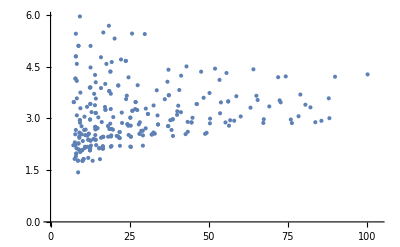

```mathematica
statsX=Select[stats,#[[1]]>=50&];
ListPlot[{Sqrt[#[[1]]],#[[2]]}&/@statsX]
```

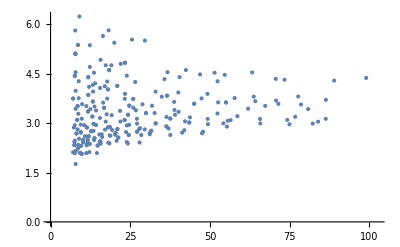

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{Sqrt[#[[3]]],#[[4]]}&/@statsX]
```

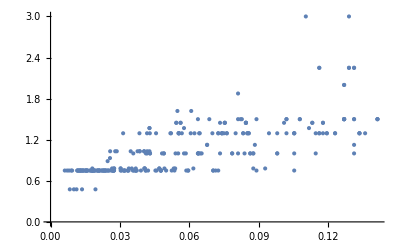

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{1/Sqrt[#[[3]]],#[[5]]}&/@statsX]
```

## Sanity Check

```mathematica
(* Usage example *)
ADUpToLevel[2,24][[1;;5]]
ADUpToLevel[3,16][[1;;5]]
ADUpToLevel[4,15][[1;;5]]
```

{{0,17990},{0.47546,26},{0.75,1302},{0.7804,610},{0.82568,2}}

{{0,2544},{0.83324,8},{0.85942,72},{1.03884,4},{1.1305,4}}

{{0,2051},{0.88412,10},{1.27864,6},{1.29666,16},{1.31934,6}}

```mathematica
(* Sanity check *)
NumAllStatesUpToLevel[2,24]
NumAllStatesUpToLevel[3,16]
NumAllStatesUpToLevel[4,15]
```

17990

2544

2051